```mathematica
(*
Assuming our data is standardized with x values in [-1,1], reasonable length scales l should always be much smaller than 20,
in which case
Exp[-1/l^2]BesselI[0,1/l^2]
and
Exp[-1/l^2]BesselI[1,1/l^2]
are very well behaved
*)
```

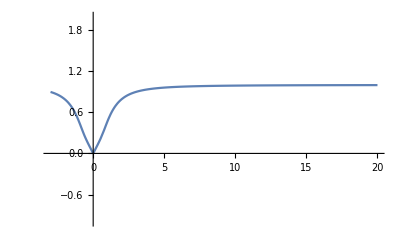

1

```mathematica
Plot[Exp[-1/l^2]BesselI[0,1/l^2],{l,-3,20},PlotRange->{-1,2}]
Limit[Exp[-1/l^2]BesselI[0,1/l^2],l->∞]
Plot[Exp[-1/l^2]BesselI[1,1/l^2],{l,-3,20},PlotRange->{-1,2}]
Limit[Exp[-1/l^2]BesselI[1,1/l^2],l->∞]
```

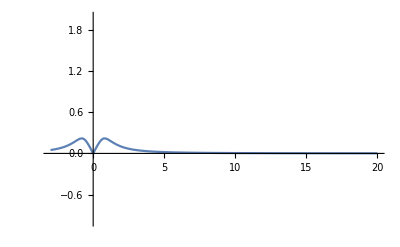

0

1

-Graphics-

0